```mathematica
Quit[]
```

```mathematica
$LoadAddOns={"FeynArts","FeynHelpers"};
Needs["FeynCalc`"]
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 1.3.0, for more information see the accompanying publication.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
CKM = IndexDelta;
Neglect[ME] = Neglect[ME2] = 0;
$FAVerbose=1;
(* use generic model from FeynCalc! The SUNF and SUNT functions in the .mod file have to be replaced by FASUNF and FASUNT *)
SetOptions[InsertFields, Model ->"../../Models/SMS-stop-FA/SMS-stop-FA",ExcludeParticles->{S[1]},InsertionLevel-> {Particles}];
SetOptions[Paint, PaintLevel -> {Particles}];
SetOptions[CreateTopologies, ExcludeTopologies -> {TadpoleCTs,Tadpoles, WFCorrectionCTs,SelfEnergyCTs}];
```

## g g → t t (1-loop)

```mathematica
tops0 = CreateTopologies[0,2->2,  ExcludeTopologies -> {TadpoleCTs,Tadpoles,WFCorrectionCTs,WFCorrections}]; 
tops = CreateTopologies[1,2->2,  ExcludeTopologies -> {TadpoleCTs,Tadpoles,WFCorrectionCTs,WFCorrections}];
processGGT =  { V[4],V[4]} -> {F[9],-F[9]};
allDiags = InsertFields[Join[tops0,tops],processGGT, InsertionLevel-> {Particles},ExcludeParticles->{V[3],V[1],S[1],S[2],S[3],V[2],F[1],F[2],F[3],F[4],F[5],F[6],F[7],F[8]}];
```

in total: 60 Particles insertions

```mathematica
amp=FCFAConvert[CreateFeynAmp[allDiags,PreFactor->1,Truncated->False]/.{SUNT->FASUNT},IncomingMomenta->{k1,k2},OutgoingMomenta->{p1,p2},LoopMomenta->{q},List->True,DropSumOver->True,SMP->True,LorentzIndexNames-> {μ,ν},Contract->True,UndoChiralSplittings->True,FinalSubstitutions-> (M$FACouplings//.{GS->gs}),ChangeDimension->D]/.{GS->gs};
nonZero={};
(* Keep only the diagrams up to gs^2 and containing yDM *)
For[n=1,n≤Length[amp],++n,
	M = Take[amp,{n}];
	M = SUNSimplify[M];
	M=Normal[Series[M,{gs,0,2}]];
	M=Normal[Series[M,{yDM,0,2}]];
	M=DiracSimplify[M];
    If[!M==={0} && !FreeQ[M,yDM] ,AppendTo[nonZero,n]];
];
```

in total: 60 Particles amplitudes

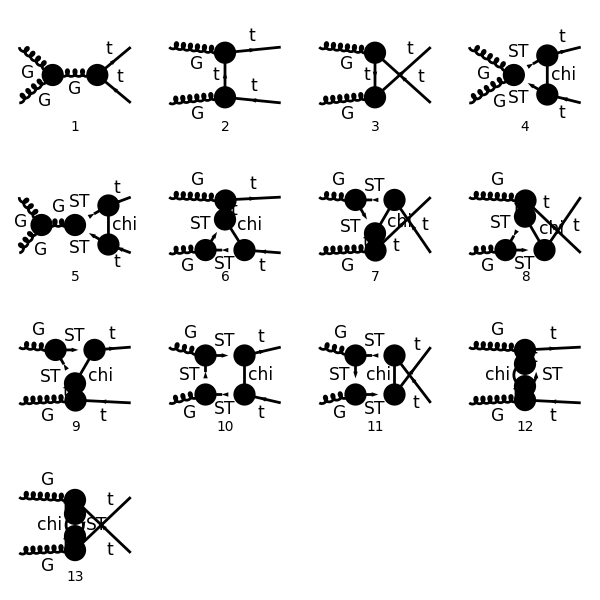

```mathematica
goodDiags=DiagramExtract[allDiags,nonZero];
(* goodDiags=DiagramExtract[goodDiags,{2,3,6,7,8,9}]; *)
(* goodDiags=DiagramExtract[goodDiags,{1,5}]; *)
(* goodDiags=DiagramExtract[goodDiags,{10,11}]; *) 
Paint[goodDiags,ColumnsXRows->{4,4},ImageSize->{ 600,600},PaintLevel->{Particles},Numbering->Simple,AutoEdit->True, SheetHeader->None];
```